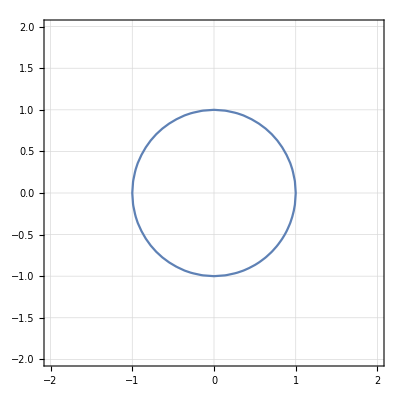

```mathematica
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2},GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}]
```

```mathematica
l[t_]:={4Cos[t],2Sin[t]};
```

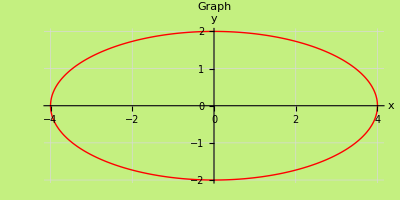

```mathematica
elipse=ParametricPlot[l[t],{t,0,2π},Background->RGBColor[0.77,0.94,0.5],PlotStyle->{Thick,Red},AxesLabel->{"x","y"},PlotLabel->"Graph",GridLines->Automatic,GridLinesStyle->{{Gray, Dotted,Blue}, {Gray, Dotted,Blue}}]
```

```mathematica
a1=ContourPlot[x^2/4+y^2/9==1,{x,-3,3},{y,-4,4},AspectRatio->Automatic,GridLines->Automatic];
```

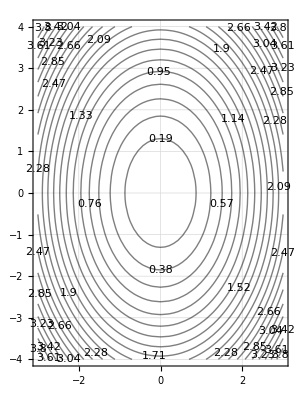

```mathematica
a2=ContourPlot[x^2/4+y^2/9,{x,-3,3},{y,-4,4},AspectRatio->Automatic,GridLines->Automatic,ContourShading->False,Contours->20,ContourLabels->True]
```

```mathematica
DSolve[y'[x]==1/(x^2 y[x]),y[x],x]
```

{{y[x]→-(√2 √(-1+x C[1]))/(√x)},{y[x]→(√2 √(-1+x C[1]))/(√x)}}

```mathematica
h[x_,y_]:=y^2/2+1/x;
```

```mathematica
sols=ContourPlot[h[x,y],{x,.5,1.5},{y,1,3},ContourShading->False,ContourLabels->True,Contours->10,GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}},Background->RGBColor[0.5,0.5,0.77,0.52]];
```

```mathematica
contour3=ContourPlot[h[x,y]==3,{x,.5,1.5},{y,1,3},ContourStyle->{Thick,Blue}];
```

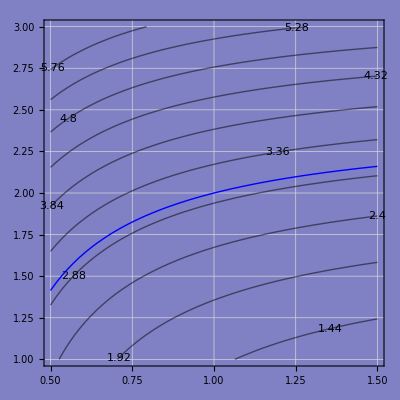

```mathematica
Show[sols,contour3]
```

```mathematica
v[x_,y_]:={y,1/x^2}
```

```mathematica
Subscript[v, 2]/Subscript[v, 1]=1/(x^2 y), Subscript[v, 2]=1/x^2; Subscript[v, 1]=y
```

```mathematica
field =StreamPlot[{y,1/x^2},{x,.5,1.5},{y,1,3}];
```

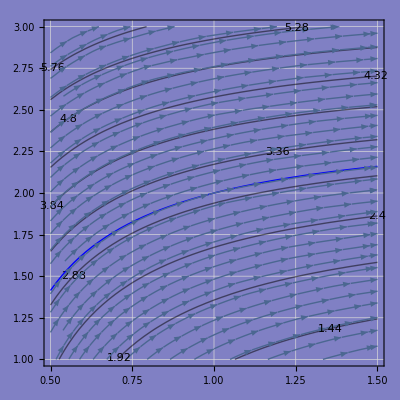

```mathematica
Show[sols,contour3,field]
```

```mathematica
circ[t_]:={Cos[t],Sin[t],Cos[t]^2};
```

```mathematica
graphCirc=ParametricPlot3D[circ[t],{t,0,2π}]
```

-Graphics3D-

```mathematica
Manipulate[Show[graphCirc,Graphics3D[{PointSize[Large],Point[circ[t]]}],Graphics3D[Arrow[{circ[t],circ[t]+.3circ'[t]}]]],{t,0,2π}]
```

```mathematica
Export["vec.gif",Manipulate[Show[graphCirc,Graphics3D[{PointSize[Large],Point[circ[t]]}],Graphics3D[Arrow[{circ[t],circ[t]+.3circ'[t]}]]],{t,0,2π}]]
```

vec.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["vec.gif"]]]
```

```mathematica
vec=Graphics[Arrow[{circ[t],circ[t]+.5circ'[t]}]];
```

```mathematica
sphere=ParametricPlot3D[Cos[λ]{Cos[θ],Sin[θ],0}+{0,0,Sin[λ]},{θ,-π,π},{λ,-π/2,π/2},PlotStyle->{Opacity[.5],Green}]
```

-Graphics3D-